```mathematica
Bogdan Chwaliński
Zestaw 8 zadanie 2
```

```mathematica
f[{x_,y_}]=(1-x)^2+100 (y-x^2)^2;
```

```mathematica
FindMinimum[(1-x)^2+100 (y-x^2)^2,
			{x,0.1},
			{y,0.1},
			Method->"LevenbergMarquardt"
	]
```

{0.,{x→1.,y→1.}}

```mathematica
FindMinimum[(1-x)^2+100 (y-x^2)^2,
			{x,0.5},
			{y,0.1},
			Method->"LevenbergMarquardt"
	]
```

{0.,{x→1.,y→1.}}

```mathematica
FindMinimum[(1-x)^2+100 (y-x^2)^2,
			{x,1.5},
			{y,2.1},
			Method->"LevenbergMarquardt"
	]
```

{0.,{x→1.,y→1.}}

```mathematica
FindMinimum[(1-x)^2+100 (y-x^2)^2,
			{x,Random[]},
			{y,Random[]},
			Method->"LevenbergMarquardt"
	]
```

{0.,{x→1.,y→1.}}

```mathematica
i = 0;
```

```mathematica
pts = Reap[FindMinimum[
(1-x)^2+100 (y-x^2)^2,
{x,0.1},{y,0.1},
Method->"LevenbergMarquardt",
StepMonitor:>{Sow[{x,y}],i++}
]][[2,1]];
Print["Potrzeba ", i ," krokow."];
pts =Join[{{-1.2,1}},pts];
```

Potrzeba 9 krokow.

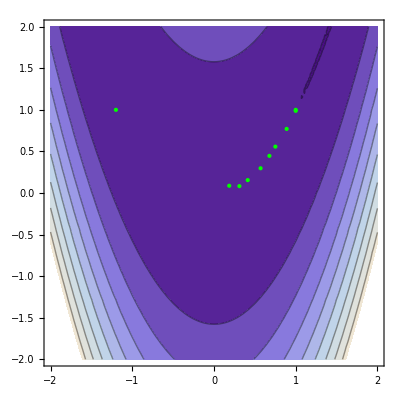

```mathematica
ContourPlot[100 (y-x^2)^2+(1-x),
			{x,-2,2},
			{y,-2,2},
			Epilog->{Green,Point[pts]}
	]
```